```mathematica
Quiet@Remove@"`*";ClearAll@"`*";
On[Assert]
SetDirectory[NotebookDirectory[]];

Row@{"Suffix: ",suffix="response"}
mcData=Import[StringJoin["mc-",suffix,".json"], "RawJSON"];
a1Data=Import[StringJoin["a1-",suffix,".json"], "RawJSON"];
a2Data=Import[StringJoin["a2-",suffix,".json"], "RawJSON"];
theoryDataT0=Import[StringJoin["theory-lT",".json"], "RawJSON"];
theoryDataT=Import[StringJoin["theory-hT",".json"], "RawJSON"];
```

Suffix: response

Sample sizes: 150

Assert::asrtf: Assertion sampleSize==Length[engyA1]&&sampleSize==Length[engyA2] failed.

150

{{True,True},{True,True},{False,True},{False,False}}

{-4.,0.,4.}

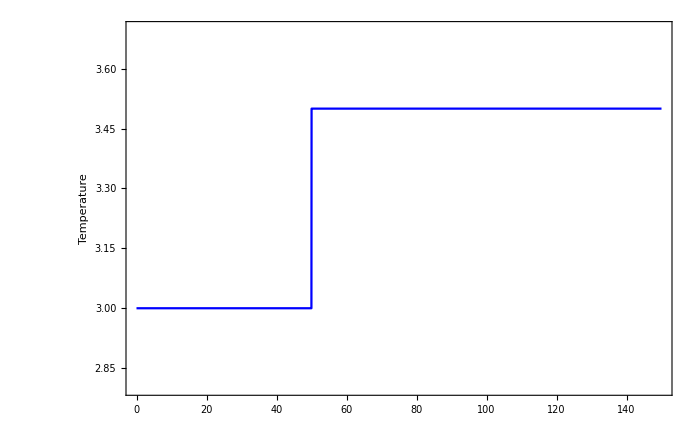

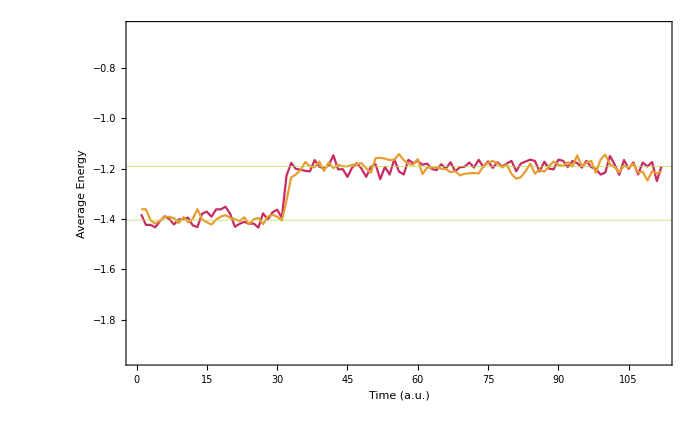

```mathematica
{engyMc, engyA1,engyA2}=#["energy_sample"]&/@{mcData, a1Data,a2Data};
Row@{"Sample sizes: ",sampleSize=Length[engyMc]}
Assert@And[
sampleSize==Length[engyA1],
sampleSize==Length[engyA2]
] 
T0 = mcData["T0"];
T = mcData["T"];
timeT0 = mcData["Length T0"] / mcData["frame_step T0"];
time = Length[engyMc]
Assert@And ={
T0 == #["T0"] &/@{a1Data, a2Data},
T == #["T"]  &/@{a1Data, a2Data},
time == Length[#]&/@{engyA1, engyA2},
timeT0 == #["Length T0"] &/@{a1Data, a2Data}
}

energyLevel = theoryDataT["energy_level"]
engyTheoryT0 = Total[theoryDataT0["energy_probs"] * energyLevel];
engyTheoryT = Total[theoryDataT["energy_probs"]*energyLevel];

colors = Table[ColorData[54][i],{i,6}];
baseStyle1 = Directive[Black, FontFamily->"Arial", FontSize->16];
baseStyle2 = Directive[Blue, FontFamily->"Arial", FontSize->16];
baseStyle3 = Directive[Red, FontFamily->"Arial", FontSize->16];

from=20;to=-20;
temperaturePlot=Plot[
Piecewise[{{T0,x<timeT0},{T,x>timeT0}}],{x,0,time},
PlotRange->{Automatic,  {T0 - 0.2, T + 0.2}},
PlotStyle->Blue,
Axes -> False,
Frame->{{True,False},{False,False}},
FrameStyle->{{Append[baseStyle2,Thickness@0.004],None},{None, None}},
FrameLabel->{{"Temperature",""},{"",""}}, 
ImageSize-> 700]


energyPlot=ListLinePlot[{engyMc[[from;;to]], engyA2[[from;;to]]},
PlotRange->{Automatic, {Min[Min[engyMc], Min[engyA2]] -0.5, Max[Max[engyMc],Max[engyA2]] + 0.5}},
PlotStyle->colors,
Axes->False,
GridLines->{{}, {engyTheoryT0, engyTheoryT}},
GridLinesStyle->Directive[colors[[4]], Thick],
Epilog->{
Inset[Framed[
SwatchLegend[
Directive[EdgeForm@None,FaceForm@#]&/@colors,
{"MC","A1","A2"},
LegendLayout->"Row",LabelStyle->baseStyle1
],FrameStyle->Append[baseStyle1,Thickness@1],RoundingRadius->5
],Scaled@{0.2,0.9}]
},
Frame->{{True,False},{True,False}},
FrameStyle->{{Append[baseStyle3,Thickness@0.004],None},{Append[baseStyle1,Thickness@0.004],None}},
FrameLabel->{{"Average Energy",""},{"Time (a.u.)",""}}, 
ImageSize->700]
```